```mathematica
m=2500;
s=50;
p=20;
(*sigma s is given by main peak position m, gain and tail fall parameter p can be varied*)
```

```mathematica
Manipulate[Plot[Exp[(x-m)/(s*p)]*Erfc[(x-m)/(Sqrt[2]*s)+1/(Sqrt[2]*p)],{x,0,3000},PlotRange-> {{100,3000},{0,2}}],{p,1,100}]
(*Kakus function*)
```

```mathematica
Manipulate[Plot[Exp[(x-m)/p] Erfc[(x-m)/(√2 s)+s/(√2 p)],{x,500,800},PlotRange-> {{500,800},{0,1}}],{p,1,25}]
(*function from SDD paper*)
```

```mathematica
Integrate[Exp[(x-ma)/pa] Erfc[(x-ma)/(√2 sa)+sa/(√2 pa)],{x,-10,10}]
```

-ⅇ^(-sa^2/(2 pa^2)) pa Erf[(-10+ma)/(√2 sa)]+pa (ⅇ^(-sa^2/(2 pa^2)) Erf[(10+ma)/(√2 sa)]+ⅇ^(-(10+ma)/pa) (ⅇ^(20/pa) Erfc[(10 pa-ma pa+sa^2)/(√2 pa sa)]-Erfc[(-(10+ma) pa+sa^2)/(√2 pa sa)]))

```mathematica
Import["VIP2energyHistogram.txt","data"]
```

Import::nffil: File not found during Import.

$Failed

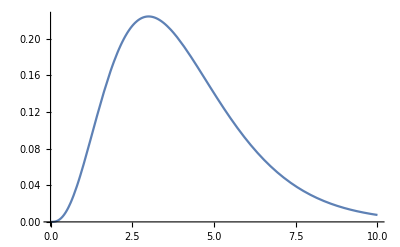

```mathematica
Plot[x^3*Exp[-x]/6,{x,0,10}]
```